```mathematica
(* Sigmoidal function: *)
S[x_]:=1/(1+ⅇ^-x)
```

```mathematica
Subscript[S, algebraic][x_]:= x/(√(1+x^2))
```

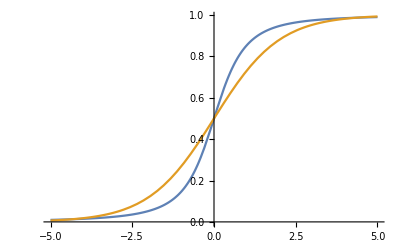

```mathematica
Plot[{Subscript[S, algebraic][x]/2+1/2, S[x]}, {x, -5,5}]
```

```mathematica
(* Scaled up version: *)
f[x_, s_:0]:= 10^s x/(√(10^(2s)+x^2))
```

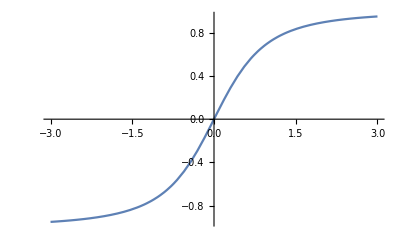

```mathematica
Plot[f[x, 0], {x,-3,3}]
```

```mathematica
f[1,0]//N
```

0.707107

```mathematica
f[10^6,6]//N
```

707107.

```mathematica
f[x_, s_:0]:= 10^s x/(2 √(10^(2 s)+x^2))+10^s/2
```

```mathematica
f[10^6,6]//N
```

853553.

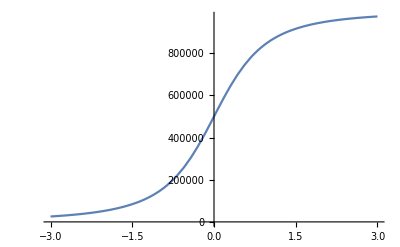

```mathematica
Plot[f[x 10^6,6], {x, -3,3}]
```